```mathematica
E=Subscript[β, 2]/γ/Subscript[T, 0]^2
```

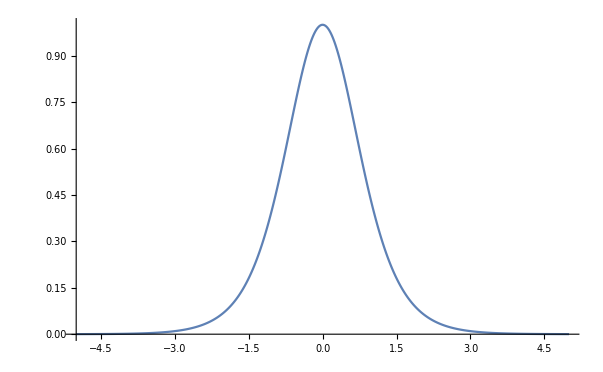

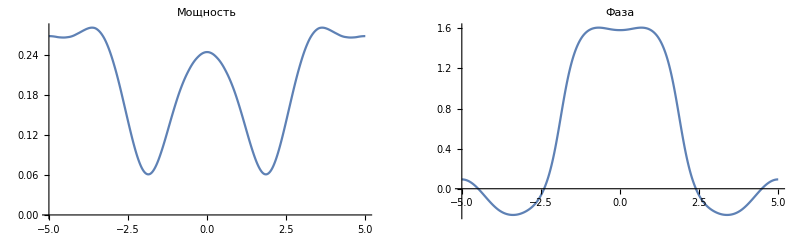

```mathematica
CalcWindow=5;(*ps*)
N0=2047;
h=0.0002;

N0=N0+Boole[EvenQ[N0]];
Sech2Imp[T0_]:=Table[N[Sech[t/T0]],{t,- CalcWindow, CalcWindow,2CalcWindow/(N0-1)}];

β2=-22;γ=1.25;
Imp=Fourier[Sech2Imp[1]];

D2Fourier=Table[-(Pi k/CalcWindow)^2,{k,0,N0/2}]~Join~Table[-(Pi (k-N0)/CalcWindow)^2,{k,Ceiling[N0/2],N0-1}];
FourierOp=Exp[-I β2/2 D2Fourier h];
SpatialOp[x_List]=Exp[I γ Abs[x]^2 h];

ListPlot[(Abs[InverseFourier[Imp]]^2),PlotRange->All,Joined->True,DataRange->{-CalcWindow, CalcWindow},AxesOrigin->{-CalcWindow,0}]

Imp=Sqrt[FourierOp]Imp;
Monitor[
For[ξ=h/2,ξ<1,ξ+=h,

Imp=InverseFourier[Imp];
Imp=Imp SpatialOp[Imp];
Imp=Fourier[Imp];
Imp=FourierOp Imp

],ξ]
Imp=InverseFourier[Imp/Sqrt[FourierOp]];

GraphicsRow[{ListPlot[(Abs[Imp]^2),PlotRange->All,Joined->True,DataRange->{-CalcWindow,CalcWindow},AxesOrigin->{-CalcWindow,0},PlotLabel->"Мощность"],ListPlot[(Arg[Imp]),PlotRange->All,Joined->True,DataRange->{-CalcWindow,CalcWindow},AxesOrigin->{-CalcWindow,0},PlotLabel->"Фаза"]},ImageSize->Full]
```

Домашнее задание
1) Усовершенствовать SSFT алгоритм так, чтобы:
он включал в себя усиление
выводился спектр излучения после обсчета
выводилась мгновенная частота ∂φ/∂t
на вход можно было подать гауссовый импульс
спектральную фильтрацию (Подсказка: расписать НУШ с комплексной дисперсией)

Подать на вход волокна γ=0.0058 1/(W m) β2=0.025 ps^2/m g=1.9 1/m (по мощности) гауссов импульс с энергией 12 pJ Tfwhm=1 ps. Вывести импульс, спектр и мгновенную частоту импульса через 6 м волокна. Посмотреть, что происходит с импульсом при спектральной фильтрации в волокне.